# Disease transmission and introgression can explain the long-lasting contact zone of modern humans and Neanderthals (Greenbaum et al. 2019)

## Two-time-scales Model

This code provides numeric solutions for P_i, β_ij, and D_i, for tmax time-steps, for the model described by Equations 1-15 in the main text of Greenbaum et al. (2019)
The translation of the input parameters in the code to those in the equations are as follows: c=c; gg=γ; aa=a; bb=b
Note that we assume a_ij=a and b_ij=b in equations (10)-(13), as was done for generating the figures in Greenbaum et al. (2019)
The starting conditions for P_i are: P10=P_1(0) and P20=P_2(0)
The starting conditions for β_ij are B110=β_11(0), B220=β_22(0), B120=β_12(0), and B210=β_21(0)

```mathematica
(*This is the two species SIR model (Equations (3)-(8)). Intiated with Subscript[I, 1](0)=0.01. Returns an approximation of Subscript[F, i] , Equation 9*)
Rinf[bmat_,gg_,tmax_]:=Module[{t,s,eq1,eq2,eq3,eq4,eq5,eq6,in1,in2,in3,in4,in5,in6,r2},
eq1=S1'[t]==-bmat⟦1,1⟧ S1[t] I1[t]-bmat⟦1,2⟧ S1[t] I2[t];(*Equation (3)*)
eq2=S2'[t]==-bmat⟦2,2⟧ S2[t] I2[t]-bmat⟦2,1⟧ S2[t] I1[t];(*Equation (4)*)
eq3=I1'[t]==bmat⟦1,1⟧ S1[t] I1[t]+bmat⟦1,2⟧ S1[t] I2[t]-gg I1[t];(*Equation (5)*)
eq4=I2'[t]==bmat⟦2,2⟧S2[t] I2[t]+bmat⟦2,1⟧ S2[t] I1[t]-gg I2[t];(*Equation (6)*)
eq5=R1'[t]==gg I1[t];(*Equation (7)*)
eq6=R2'[t]==gg I2[t];(*Equation (8)*)
in1=S1[0]==0.99;
in2=S2[0]==1;
in3=I1[0]==0.01;
in4=I2[0]==0;
in5=R1[0]==0;
in6=R2[0]==0;
s=NDSolve[{eq1,in1,eq2,in2,eq3,in3,eq4,in4,eq5,in5,eq6,in6},{S1[t],S2[t],I1[t],I2[t],R1[t],R2[t]},{t,0,tmax}];
r2=Evaluate[R2[t]/.s]⟦1⟧/. t->tmax;(*Equation (9)*)
r2
]
Runmodel[P10_,P20_,B110_,B220_,B120_,B210_,gg_,c_,aa_,bb_,tmax_]:=Module[{DB1,DB2,Reslist,a11,a22,a12,a21,b11,b22,b12,b21,B11,B22,B12,B21,P1,P2,tau},
a11=aa;a22=aa;a12=aa;a21=aa;(*Subscript[a, ij]=a in Equations (10)-(13)*)
b11=bb;b22=bb;b12=bb;b21=bb;(*Subscript[b, ij]=b in Equations (10)-(13)*)
B11=B110;B22=B220;B12=B120;B21=B210;
P1=P10;P2=P20;
tau=1000;(*τ=1000 in Equation 9. Could be increased to improve estimation of Subscript[F, i]*)
DB1=Rinf[{{B22,B12},{B21,B11}},gg,tau]*P2;
DB2=Rinf[{{B11,B21},{B12,B22}},gg,tau]*P1;
Reslist={{P1,P2,B11,B12,B21,B22,DB1,DB2,Rinf[{{B11,B21},{B12,B22}},gg,1000],Rinf[{{B22,B12},{B21,B11}},gg,1000],Max[Eigenvalues[1/gg{{B22,B12},{B21,B11}}]]}};
Do[
P1=Max[P1-c B12,0];(*Equation (14)*)
P2=Max[P2-c B21,0];(*Equation (15)*)
B11=Max[B11-a11 DB1+b11(B110-B11),0];(*Equation (10)*)
B22=Max[B22-a22 DB2+b22(B220-B22),0];(*Equation (11)*)
B12=Max[B12-a12 DB2 +b12(B120-B12),0];(*Equation (12)*)
B21=Max[B21-a21 DB1 +b21(B210-B21),0];(*Equation (13)*)
DB1=Rinf[{{B22,B12},{B21,B11}},gg,tau]*P2;(*Equation (1)*)
DB2=Rinf[{{B11,B21},{B12,B22}},gg,tau]*P1;(*Equation (2)*)
AppendTo[Reslist,{P1,P2,B11,B12,B21,B22,DB1,DB2,Rinf[{{B11,B21},{B12,B22}},gg,1000],Rinf[{{B22,B12},{B21,B11}},gg,1000],Max[Eigenvalues[1/gg{{B22,B12},{B21,B11}}]]}]
,{t,1,tmax}];
Reslist
]
```

This code plots the outputs of RunModel, assuming that the initial condition are symmetric (i.e. a two curves for β_ij will be shown, and a single curve will be shown for other parameters, as in Fig. 3)

```mathematica
PlotResultsSymmetric[Reslist_,ttmax_]:=Module[{p1,p2,b11,b12,b21,b22,db1,db2,Rinf1,Rinf2,R0,a1,a2,a3,gg},
p1=Flatten[Take[Reslist,All,{1}]];
p2=Flatten[Take[Reslist,All,{2}]];
b11=Flatten[Take[Reslist,All,{3}]];
b12=Flatten[Take[Reslist,All,{4}]];
b21=Flatten[Take[Reslist,All,{5}]];
b22=Flatten[Take[Reslist,All,{6}]];
db1=Flatten[Take[Reslist,All,{7}]];
db2=Flatten[Take[Reslist,All,{8}]];
Rinf1=Flatten[Take[Reslist,All,{9}]];
Rinf2=Flatten[Take[Reslist,All,{10}]];
R0=Flatten[Take[Reslist,All,{11}]];
a1=ListPlot[{b11,b21},Joined->True,PlotRange->{{0,ttmax},{0,0.05}},PlotStyle->{Directive[RGBColor["#ff1a48"],Dashed],Directive[RGBColor["#ff1a48"]]},ImageSize->250,AxesLabel->{"Time (t)","β_ij"}];
a2=ListPlot[{p1},Joined->True,PlotRange->{{0,ttmax},{0,100}},PlotStyle->RGBColor["#ff1a48"],ImageSize->250,AxesLabel->{"Time (t)","P"}];
a3=ListPlot[{db1},Joined->True,PlotRange->{{0,ttmax},{0,dbrange}},PlotStyle->RGBColor["#ff1a48"],ImageSize->250,AxesLabel->{"Time (t)","D"}];
gg=Grid[{{a1,a2,a3}}]
]
```

This code plots the outputs of RunModel, assuming that the initial condition are asymmetric (i.e. a four curves for β_ij will be shown, and two curves will be shown for other parameters, as in Fig. 4)

```mathematica
PlotResultsAsymmetric[Reslist_,ttmax_]:=Module[{p1,p2,b11,b12,b21,b22,db1,db2,Rinf1,Rinf2,R0,a1,a2,a3,a4,gg},
p1=Flatten[Take[Reslist,All,{1}]];
p2=Flatten[Take[Reslist,All,{2}]];
b11=Flatten[Take[Reslist,All,{3}]];
b12=Flatten[Take[Reslist,All,{4}]];
b21=Flatten[Take[Reslist,All,{5}]];
b22=Flatten[Take[Reslist,All,{6}]];
db1=Flatten[Take[Reslist,All,{7}]];
db2=Flatten[Take[Reslist,All,{8}]];
Rinf1=Flatten[Take[Reslist,All,{9}]];
Rinf2=Flatten[Take[Reslist,All,{10}]];
R0=Flatten[Take[Reslist,All,{11}]];
a1=ListPlot[{b11,b22},Joined->True,PlotRange->{{0,ttmax},{0,Max[b11,b22,b12,b12]*1.1}},PlotStyle->Dashed,ImageSize->250,AxesLabel->{"Time (t)","β_ij"}];
a2=ListPlot[{b21,b12},Joined->True,PlotRange->{{0,ttmax},{0,Max[b11,b22,b12,b12]*1.1}},ImageSize->250,AxesLabel->{"Time (t)","β_ij"}];
a3=ListPlot[{p2,p1},Joined->True,PlotRange->{{0,ttmax},All},ImageSize->250,AxesLabel->{"Time (t)","P"}];
a4=ListPlot[{db1,db2},Joined->True,PlotRange->{{0,ttmax},All},ImageSize->250,AxesLabel->{"Time (t)","D"}];
gg=Grid[{{Show[a1,a2],a3,a4}}]
]
```

For example:

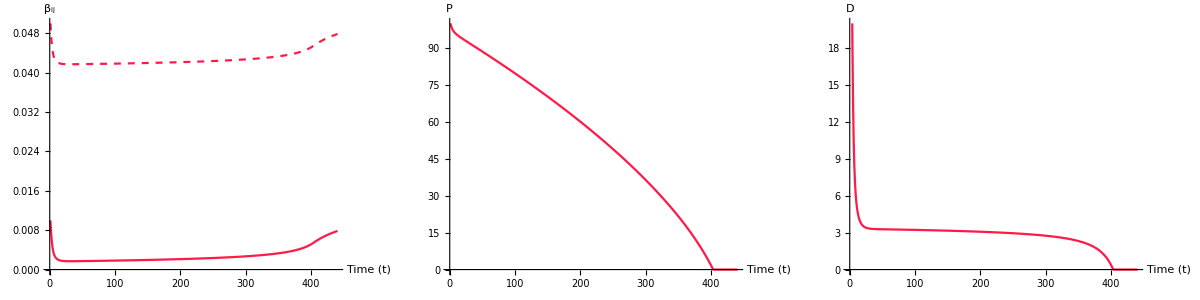

```mathematica
tmax=440;
Reslist=Runmodel[100,100,0.05,0.05,0.01,0.01,0.045,100,5*10^-5,0.02,tmax];(*p1,p2,b11,b22,b21,b12,γ,c,a,b,tmax*)
plot1=PlotResultsSymmetric[Reslist,tmax]
```

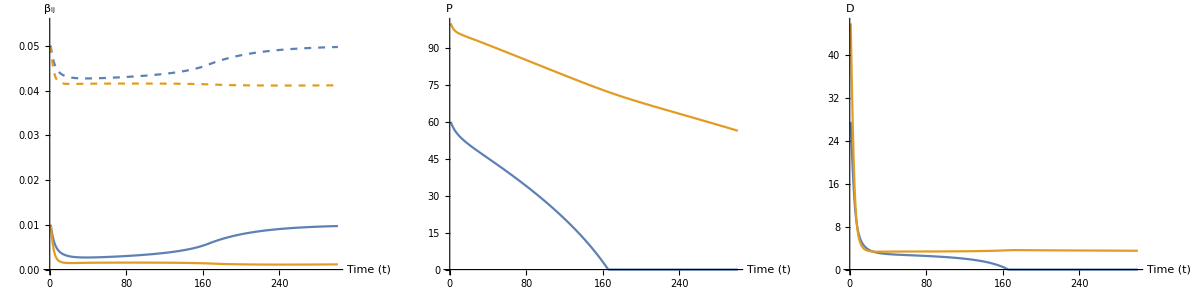

```mathematica
tmax=300;
Reslist=Runmodel[100,60,0.05,0.05,0.01,0.01,0.045,100,tmax];(*p1,p2,b11,b22,b21,b12,γ,c,a,b,tmax*)
plot2=PlotResultsAsymmetric[Reslist,tmax]
```

## Single-time-scale Model

This code provides numeric solutions for N_i, I_i, and α_i, for tmax time-steps, for the model described by Equations 16-22 in the main text of Greenbaum et al. (2019)
The translation of the parameters in the code to those in the equations are as follows: b11=β_11; b22=β_22; ba=β_a; cc=c; mu=μ; KK=K; LL=λ
The starting conditions for α_i are: a10=α_1(0) and a20=α_2(0)
The starting conditions for I are I_1(0)=I_2(0)=0
The starting conditions for N are explained in the methods section in the main text (N_i(0)=K(λ-μ)/μ)

```mathematica
RunModel[b11_,b22_,ba_,cc_,mu_,KK_,LL_,a10_,a20_,tmax_]:=Module[{a1,a2,L1,L2,K1,K2,mu1,mu2,c1,c2,eq1,eq2,eq3,eq4,eq5,eq6,in1,in2,in3,in4,in5,in6,s},
L1=LL; (*Intrinsic recruitment rate*)
L2=LL;
K1=KK;  (*half reduction in reruitment rate*)
K2=KK;
mu1=mu;(*Natural death rate*)
mu2=mu;
c1=cc;(*Disease transmission/introgression ratio*)
c2=cc;

eq1=N1'[t]==(L1 N1[t])/(K1+N1[t])-mu1 N1[t]-aa1[t] I1[t];(*Equation (17)*)
eq2=N2'[t]==(L2 N2[t])/(K2+N2[t])-mu2 N2[t]-aa2[t] I2[t];(*Equation (18)*)
eq3=I1'[t]==(N1[t]-I1[t])(ba N2[t]+b11 I1[t])-(mu1+aa1[t])I1[t];(*Equation (19)*)
eq4=I2'[t]==(N2[t]-I2[t])(ba N1[t]+b22 I2[t])-(mu2+aa2[t])I2[t];(*Equation (20)*)
eq5=aa1'[t]==-c1 ba N2[t]*If[aa1[t]>0,1,0] ;(*Equation (21)*)
eq6=aa2'[t]==-c2 ba N1[t]*If[aa2[t]>0,1,0] ;(*Equation (22)*)
in1=N1[0]==K1 (L1-mu1)/mu1;(*Intial condition for N: Subscript[N, i](0)=K(λ-μ)/μ*)
in2=N2[0]==K2 (L2-mu2)/mu2;(*Intial condition for N: Subscript[N, i](0)=K(λ-μ)/μ*)
in3=I1[0]==0;
in4=I2[0]==0;
in5=aa1[0]==a10;
in6=aa2[0]==a20;
s=NDSolve[{eq1,in1,eq2,in2,eq3,in3,eq4,in4,eq5,in5,eq6,in6},{N1[t],N2[t],I1[t],I2[t],aa1[t],aa2[t]},{t,0,tmax}]
]
```

This code plots the outputs of RunModel, assuming that the initial condition are symmetric (i.e. a single curve will be shown, as in Fig. 5B-D)

```mathematica
PlotSymmetric[s_,tmax_]:=Module[{g1,g2,g3,g4,s1},
g1=Plot[{Evaluate[N1[t]/.s](*,Evaluate[N2[t]/.s]*)},{t,0,tmax},PlotRange->{0,2},ImageSize->250,PlotStyle->RGBColor["#ff1a48"],AxesLabel->{"Time (t)","N"}];
g2=Plot[{Evaluate[I1[t]/.s](*,Evaluate[I2[t]/.s]*)},{t,0,tmax},PlotRange->All,ImageSize->250,PlotStyle->RGBColor["#ff1a48"],AxesLabel->{"Time (t)","I"}];
g3=Plot[{Evaluate[aa1[t]/.s](*,Evaluate[a2[t]/.s]*)},{t,0,tmax},PlotRange->{0,1},ImageSize->250,PlotStyle->RGBColor["#ff1a48"],AxesLabel->{"Time (t)","α"}];
g4=Plot[{Evaluate[aa1[t]/.s]*Evaluate[I1[t]/.s]},{t,0,tmax},PlotRange->All,ImageSize->250,PlotStyle->RGBColor["#ff1a48"],AxesLabel->{"Time (t)","α*I"}];
s1=Grid[{{g1,g3,g4}}]
]
```

This code plots the outputs of RunModel, assuming that the initial condition are asymmetric (i.e. two curve will be shown, as in Fig. 5E-G)

```mathematica
PlotAsymmetric[s_,tmax_]:=Module[{g1,g2,g3,g4,s1},
g1=Plot[{Evaluate[N1[t]/.s],Evaluate[N2[t]/.s]},{t,0,tmax},PlotRange->All,ImageSize->250,AxesLabel->{"Time (t)","N"}];
g2=Plot[{Evaluate[I1[t]/.s],Evaluate[I2[t]/.s]},{t,0,tmax},PlotRange->All,ImageSize->250,AxesLabel->{"Time (t)","I"}];
g3=Plot[{Evaluate[aa1[t]/.s],Evaluate[aa2[t]/.s]},{t,0,tmax},PlotRange->{0,1},ImageSize->250,AxesLabel->{"Time (t)","α"}];
g4=Plot[{Evaluate[aa1[t]/.s]*Evaluate[I1[t]/.s],Evaluate[aa2[t]/.s]*Evaluate[I2[t]/.s]},{t,0,tmax},PlotRange->All,ImageSize->250,AxesLabel->{"Time (t)","α*I"}];
s1=Grid[{{g1,g3,g4}}]
]
```

For example:

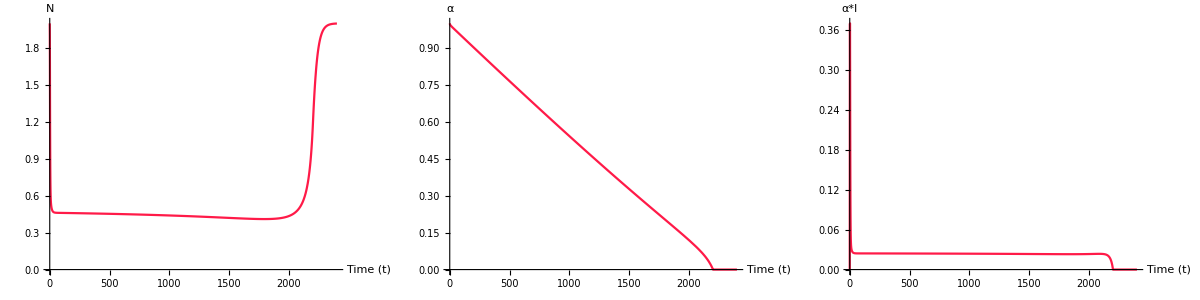

```mathematica
tmax=2400;
res=RunModel[0.5,0.5,0.1,0.01,0.05,1,0.15,1,1,tmax];
plot1==PlotSymmetric[res,tmax]
```

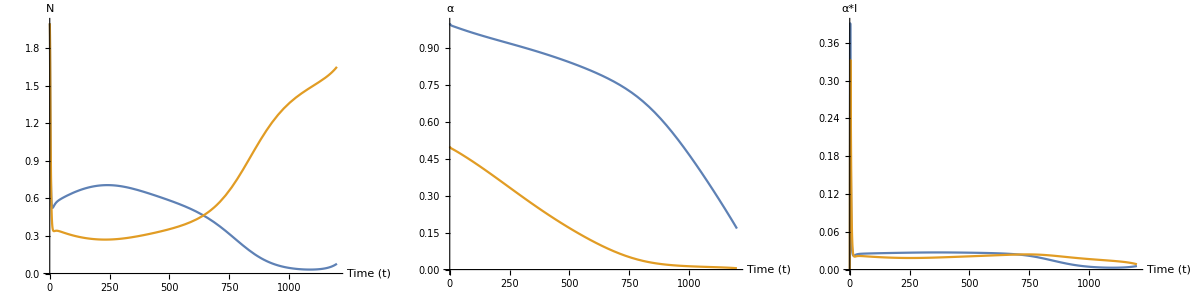

```mathematica
tmax=1200;
res=RunModel[0.5,0.5,0.1,0.01,0.05,1,0.15,1,0.5,tmax];
plot2=PlotAsymmetric[res,tmax]
```